# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
cityType=RandomChoice[Range[classesNumber],citiesNumber]
```

{1,1,2,2,1,2,2,2,2,1,2,2,1,2,1,1,2,1,2,1,2,1,2,2,2,1,1,1,1,2,1,1,2,2,2,2,1,1,2,1,2,2,2,2,1,1,2,2,1,1}

```mathematica
{vertexSize,vertexLabelSize}={2.5,7.5};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={50,100,2};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
directionStrength=.99;
movementProbabilitiesVector={1-directionStrength,directionStrength};
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0.01 | 0.99
0.99 | 0.01)

## Generate Random Spatial Setting

{{1,2,5,6,8,15,16,17,18,20},{3,4},{7,10},{9},{11,12,13},{14},{19},{21},{22,23},{24,25,26,28,29,41},{27},{30,31,42,43},{32,33,34,35,36},{37,38},{39,40},{44,45,46,47,48,49,50}}

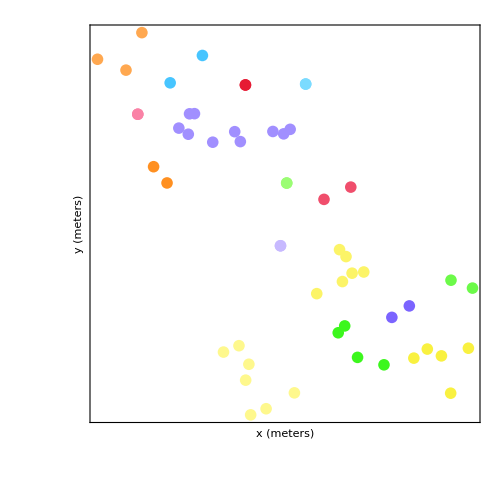

```mathematica
(*This is a very basic algorithm to generate points in a landscape. Replace it with a better later on.*)
{sampledCoordinates,names,pops,cities}=GenerateAccumulatedCoordinates[-100,citiesNumber];
distances = CalculateEuclideanDistances[sampledCoordinates];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}]
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

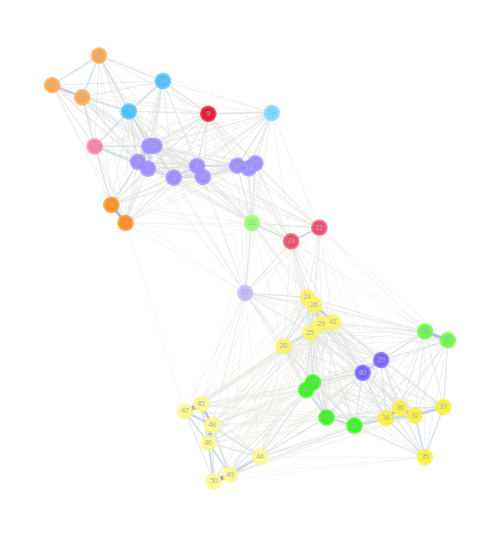

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .1];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 500,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
{cityType[[1]],#}&/@cityType;
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

Movement Network

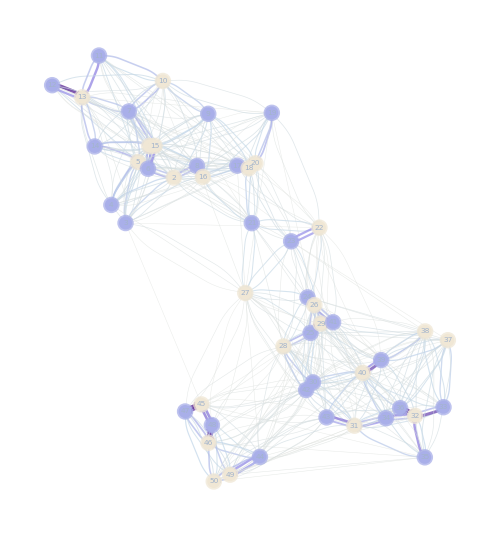

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .25,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->500,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

Sink and Source

```mathematica
differenceThreshold=.3;
(**)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=Chop[normalizedMaskedMatrix];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=Chop[normalizedMaskedMatrix]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
(**)
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Switch[#[[3]],"Bridge",Black,"Sink",Darker[Blue,0],"Source",Darker[Red,0]],Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

{{1,2,5,6,8,15,16,17,18,20},{3,4},{7,10},{9},{11,12,13},{14},{19},{21},{22,23},{24,25,26,28,29,41},{27},{30,31,42,43},{32,33,34,35,36},{37,38},{39,40},{44,45,46,47,48,49,50}}

{Sink,Source,Bridge,Bridge,Source,Bridge,Source,Bridge,Bridge,Sink,Bridge,Bridge,Source,Bridge,Bridge,Bridge}

-2.450 |  0.655 |  0.186 |  0.226 |  0.719 |  0.278 |  0.360 |  0.185 |  0.157 | -1.490 | -0.003 |  0.258 |  0.588 |  0.294 | -0.253 |  0.291
Sink | Source | Bridge | Bridge | Source | Bridge | Source | Bridge | Bridge | Sink | Bridge | Bridge | Source | Bridge | Bridge | Bridge

Sinks and Sources Report

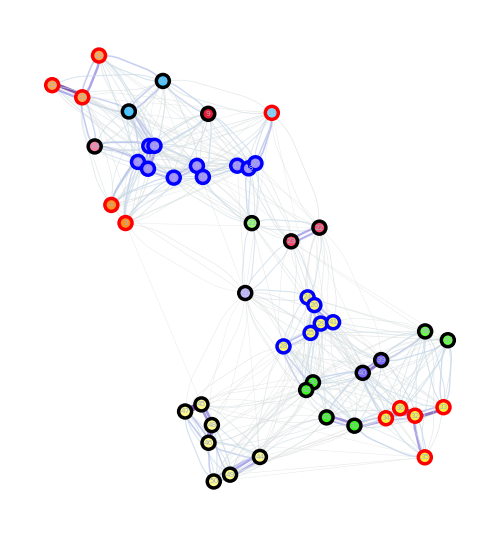
Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
-2.450 |  0.655 |  0.186 |  0.226 |  0.719 |  0.278 |  0.360 |  0.185 |  0.157 | -1.490 | -0.003 |  0.258 |  0.588 |  0.294 | -0.253 |  0.291
Sink | Source | Bridge | Bridge | Source | Bridge | Source | Bridge | Bridge | Sink | Bridge | Bridge | Source | Bridge | Bridge | Bridge

```mathematica
gridSinksAndSources=Grid[{
Style[#,25]&/@{"Clustered Map","","Point Types","","Sources (R) and Sinks(B)"},
{map,Style["+",Bold,50],graph,Style["=",Bold,50],Grid[{{graphSinkSource},{gridSourceSink}}]}
}]
```

Centrality Analysis

```mathematica
BetweennessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
BetweennessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,0.,1.,0.,0.0909091,0.0909091,0.,1.27981,1.27981,0.,0.,0.,0.666667,7.26342,49.0867,16.011,15.2831,10.1033,43.2928,11.0609,104.05,67.0659,96.8027,71.2234,18.875,18.875,193.863,23.087,23.087,13.1254,4.21203,0.,0.,1.07937,0.222222,0.422222,0.353846,1.92517,5.49964,7.2798,8.59817,6.23303,6.23303,4.34841,2.24363,0.285714,1.5,0.,0.,0.}

{67.2615,99.5908,188.011,49.9869,36.7201,16.619,12.304,94.7573,39.9467,60.8219,5.22758,5.22758,30.0214,9.83782,85.6226,112.756,85.7043,63.2106,107.649,63.2106,176.645,287.978,282.233,29.9385,63.4922,82.3648,455.18,145.62,38.0388,184.148,51.888,26.5224,6.91729,12.5435,17.4543,12.5435,52.3147,59.3465,72.4061,115.618,60.0793,142.947,87.9823,35.2164,57.5827,11.3965,26.5908,26.5908,21.788,24.146}

-Graphics-

```mathematica
ClosenessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
ClosenessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,24.5087,35.8139,20.6565,27.952,17.5126,34.1979,38.4147,40.3551,37.2262,45.109,44.7934,34.797,33.734,44.4256,42.6039,45.7697,37.9732,52.281,39.3945,48.734,50.8007,46.6234,38.9577,35.9533,29.1612,52.8407,34.6752,34.8341,38.4544,39.7926,32.4955,30.9794,29.7844,30.7463,28.9657,42.5753,41.6705,38.7246,37.0176,41.215,43.5484,41.006,45.3222,48.6125,43.8905,38.8555,37.7888,44.5678,41.514}

{8.89183,9.53264,11.4328,10.2259,8.67936,8.27123,7.5335,7.97328,9.55775,10.0134,7.94582,8.24545,8.74138,7.70585,10.139,10.6229,10.0006,8.9821,11.0723,8.51424,10.4959,11.262,10.7366,8.90944,9.61674,9.54846,12.3916,10.2683,8.09557,11.0617,8.89282,8.66105,8.25761,8.19147,9.17749,8.46452,10.3449,10.3003,9.56753,8.42962,10.2529,11.068,10.9586,10.4482,9.02459,8.35582,9.31821,9.58568,8.86557,9.17725}

-Graphics-

Walkers

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
```

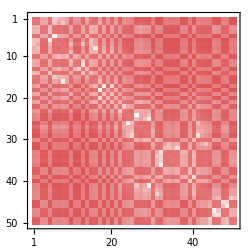
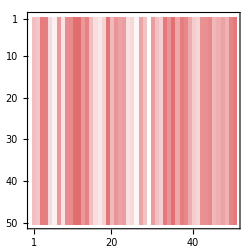
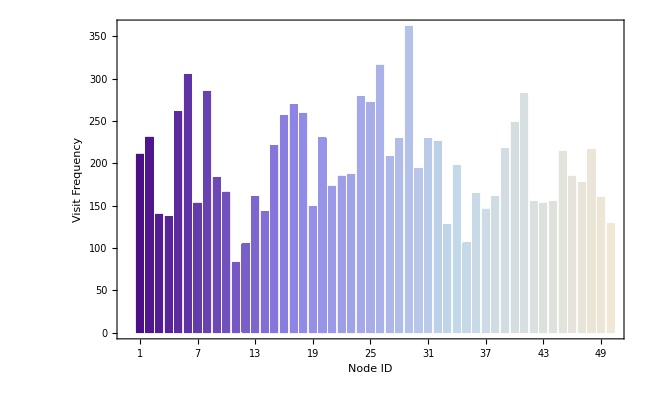
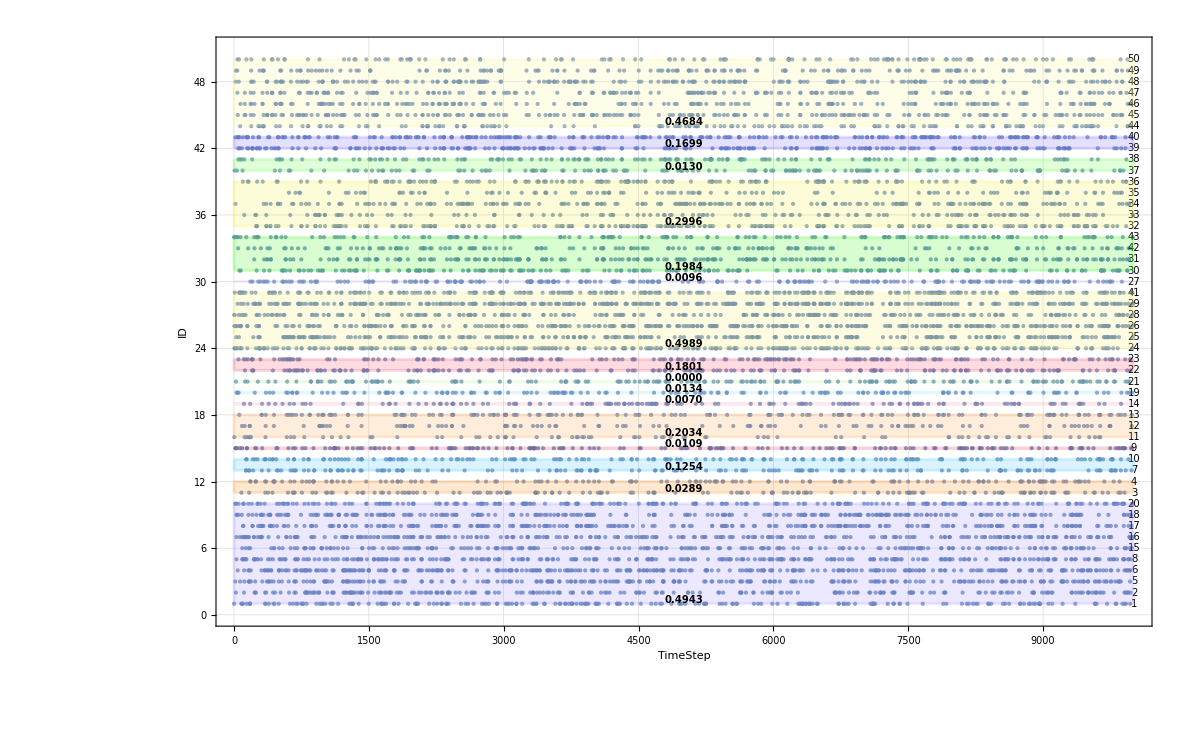
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(**)
data=RandomFunction[markov,{0,10000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->650,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
songs=ListPlotSongWithCommunities[(data//Normal)[[1,All,2]],Map[ToExpression,clustersStrings,Infinity],colors,ImageSize->1200,TextSize->10];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm;
limitMatrix=MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
transitionsMatrix=MarkovProcessProperties[markov,"TransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
matricesGrid=Grid[{Style[#,15]&/@{"Transitions","Limiting"},{transitionsMatrix,limitMatrix}}];
gridRandomWalker=Grid[{{Grid[{{matricesGrid},{barChartFrequency}}],songs}}]
```

## Export Report

```mathematica
Grid[{{gridSinksAndSources},{gridRandomWalker}}]
Export["NetworkReport"<>StringPadLeft[ToString[(directionStrength*100)//Round],3,"0"]<>".pdf",%,ImageSize->5000,ImageResolution->500]
```

Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
-2.450 |  0.655 |  0.186 |  0.226 |  0.719 |  0.278 |  0.360 |  0.185 |  0.157 | -1.490 | -0.003 |  0.258 |  0.588 |  0.294 | -0.253 |  0.291
Sink | Source | Bridge | Bridge | Source | Bridge | Source | Bridge | Bridge | Sink | Bridge | Bridge | Source | Bridge | Bridge | Bridge
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

NetworkReport099.pdf